## Import

```mathematica
SetDirectory[NotebookDirectory[]];
pathSRC="../src/";
Get[pathSRC<>"basic.m"];
Get[pathSRC<>"dftb.m"];
Get[pathSRC<>"negf.m"];
Get[pathSRC<>"xyz.m"];

Get["../skf/auorg.E.m"];
Get["../skf/auorg.V.mx"];
Get["../skf/auorg.S.mx"];
```

```mathematica
GetOrbitalΣ[Σd_]:=Module[{},
bands=(
{atomIndex,σ}=#;
Band[{orbInForAtomIn[[atomIndex]],orbInForAtomIn[[atomIndex]]}]->
σ*IdentityMatrix[MAXORB[types⟦atomIndex⟧]]
)&/@Σd;
SparseArray[bands,{norb,norb}]
]
```

```mathematica
GetLocalDOS[ee_,HC_,SC_,ΣL_,ΣR_]:=Module[{ΓL,ΓR,gr,ga,ldos,trans},
ΓL=-2Im[ΣL];
ΓR=-2Im[ΣR];
gr=Calcgs0[ee,HC+ΣL+ΣR,SC];
ga=gr†;

ldos=-1/π Diagonal[Im[gr]];
ldos
]
```

## Ham gen

```mathematica
MAXORB["Au"]=9
```

9

```mathematica
moleName="mcpp_60Au";
{atoms,types,bonds}=ImportXYZ[moleName<>".xyz"];
natom=Length[atoms]
```

178

```mathematica
h=DFTBSolver2[atoms,types];
s=DFTBSolver2[atoms,types,"S"];
```

```mathematica
(*self energy diagonal element: atom index, Im self energy[eV]*)
ΣdL=Table[{i,1},{i,102,122}];
ΣdR=Table[{i,1},{i,158,178}];
(*orbital-atom relation*)
orbInAtom=MAXORB/@types;
norb=Total[MAXORB/@types];
orbInForAtomIn=Accumulate[{1}~Join~orbInAtom][[1;;-2]];
(*self energy diagonal element applied to orbital: orbital index, Im self energy[eV]*)
ΣL=-I*GetOrbitalΣ[ΣdL];
ΣR=-I*GetOrbitalΣ[ΣdR];
```

```mathematica
(*set mol au d orbital hopping to 0*)
audorb=(orbInForAtomIn[[67]]-1+Range[5,9])~Join~(orbInForAtomIn[[123]]-1+Range[5,9])

(
onsite=h⟦#,#⟧;
h⟦1;;196,#⟧=0;
h⟦#,1;;196⟧=0;
h⟦#,#⟧=onsite(*delete cross but keep onsite*)
)&/@audorb
```

{197,198,199,200,201,701,702,703,704,705}

{-6.88939,-6.88939,-6.88939,-6.88939,-6.88939,-6.88939,-6.88939,-6.88939,-6.88939,-6.88939}

## MOL

```mathematica
atomsListM=Append[Range[1,67],123];
(*atomsListM=Range[1,66];*)
atomsM=atoms⟦atomsListM⟧;
typesM=types⟦atomsListM⟧;
hM=DFTBSolver2[atomsM,typesM];
sM=DFTBSolver2[atomsM,typesM,"S"];
{eval,evec}=MyEigensystem[{hM,sM}];
{EHOMO,ELUMO,EF,EGap,NHOMO}=GetHOLU[eval,evec,atomsM,typesM]
EF
```

{-4.33643,-4.2322,-4.28431,0.104235,107}

-4.28431

```mathematica
(*{eval,evec}=MyEigensystem[{h,s}];
{EHOMO,ELUMO,EF,EGap,NHOMO}=GetHOLU[eval,evec,atoms,types]
EF*)
```

## Highlight Contact and Molecule

```mathematica
highlightAtom=Table[
{
If[MemberQ[ΣdL⟦All,1⟧,i],clr=Red,
If[MemberQ[ΣdR⟦All,1⟧,i],clr=Blue,
If[MemberQ[atomsListM,i],clr=Orange,
clr=Gray
];
];
];
clr,
Sphere[atoms⟦i⟧]},
{i,natom}
];
```

```mathematica
Graphics3D[
highlightAtom
]
```

-Graphics3D-

## NEGF run

```mathematica
{emin,emax,estep}={EF-2,EF+2,0.04};
```

```mathematica
et=Table[
{ϵ-EF}~Join~NEGFSystemWBΣS[ϵ,h,s,ΣL,ΣR],
{ϵ,emin,emax,estep}
]
```

{{-2.,0.000887761,126.134},{-1.96,0.000909684,129.069},{-1.92,0.00113173,133.317},{-1.88,0.001979,140.83},{-1.84,0.0064379,151.668},{-1.8,0.199737,172.143},{-1.76,0.00722053,160.277},{-1.72,0.00103748,166.842},{-1.68,0.000308134,160.916},{-1.64,0.000142716,164.384},{-1.6,0.000117092,162.199},{-1.56,0.000201983,147.82},{-1.52,0.000465018,139.571},{-1.48,0.00220432,133.287},{-1.44,0.0563791,150.45},{-1.4,0.00449447,120.968},{-1.36,0.0278841,119.785},{-1.32,0.00101882,116.527},{-1.28,0.0000657715,116.866},{-1.24,0.0000122414,120.355},{-1.2,5.21191×10^-6,127.832},{-1.16,4.16203×10^-6,135.358},{-1.12,4.16214×10^-6,161.555},{-1.08,2.56966×10^-6,138.621},{-1.04,1.9338×10^-6,110.488},{-1.,1.55182×10^-6,96.7142},{-0.96,1.21061×10^-6,88.6866},{-0.92,9.02889×10^-7,82.2462},{-0.88,6.43944×10^-7,80.0712},{-0.84,4.60568×10^-7,93.3068},{-0.8,3.45277×10^-7,64.2263},{-0.76,2.74795×10^-7,53.677},{-0.72,2.31428×10^-7,48.1018},{-0.68,2.05009×10^-7,44.2329},{-0.64,1.90122×10^-7,41.3308},{-0.6,1.84065×10^-7,39.0949},{-0.56,1.85819×10^-7,37.361},{-0.52,1.95612×10^-7,36.0276},{-0.48,2.14821×10^-7,35.0266},{-0.44,2.46052×10^-7,34.3082},{-0.4,2.93195×10^-7,33.8262},{-0.36,3.61232×10^-7,33.5262},{-0.32,4.55544×10^-7,33.3362},{-0.28,5.81276×10^-7,33.1709},{-0.24,7.44777×10^-7,32.9589},{-0.2,9.59551×10^-7,32.681},{-0.16,1.2559×10^-6,32.3887},{-0.12,1.68949×10^-6,32.1818},{-0.08,2.34149×10^-6,32.1615},{-0.04,3.29298×10^-6,32.3869},{0.,4.54313×10^-6,32.8472},{0.04,5.89612×10^-6,33.4705},{0.08,7.00765×10^-6,34.195},{0.12,7.68504×10^-6,35.044},{0.16,8.03746×10^-6,36.0799},{0.2,8.24766×10^-6,37.2683},{0.24,8.33991×10^-6,38.4023},{0.28,8.19439×10^-6,39.1539},{0.32,7.72442×10^-6,39.2049},{0.36,6.99852×10^-6,38.3773},{0.4,6.18478×10^-6,36.72},{0.44,5.43763×10^-6,34.5013},{0.48,4.85412×10^-6,32.0798},{0.52,4.48419×10^-6,29.7537},{0.56,4.35448×10^-6,27.6952},{0.6,4.49504×10^-6,25.9655},{0.64,4.96923×10^-6,24.5591},{0.68,5.9146×10^-6,23.4414},{0.72,7.61931×10^-6,22.5709},{0.76,0.0000106981,21.9096},{0.8,0.0000165545,21.427},{0.84,0.000028774,21.1003},{0.88,0.0000581968,20.9155},{0.92,0.000147626,20.8729},{0.96,0.000576387,21.0378},{1.,0.0104463,23.5182},{1.04,0.00535884,22.2173},{1.08,0.00116702,21.7819},{1.12,0.000677799,22.1616},{1.16,0.000553973,22.6988},{1.2,0.000543623,23.3441},{1.24,0.000625734,24.2732},{1.28,0.000695151,24.7617},{1.32,0.000849593,25.4855},{1.36,0.00106524,26.1819},{1.4,0.00135563,26.8344},{1.44,0.00174841,27.4513},{1.48,0.0022987,28.0574},{1.52,0.0031107,28.6736},{1.56,0.00437471,29.2929},{1.6,0.00644583,29.8738},{1.64,0.0100631,30.3699},{1.68,0.0171251,30.7995},{1.72,0.0341692,31.3606},{1.76,0.0957974,32.9055},{1.8,0.572368,42.7763},{1.84,0.444022,39.3582},{1.88,0.140195,34.736},{1.92,0.132102,36.2426},{1.96,0.822485,63.4691},{2.,0.042877,39.8423}}

```mathematica
Export["transwithd.m",et];
```

```mathematica
et0=Import["transwithd.m"]
```

{{-2.,0.993853,128.61},{-1.96,0.993343,131.209},{-1.92,0.99806,135.294},{-1.88,1.00002,142.711},{-1.84,0.992647,152.894},{-1.8,0.969753,156.004},{-1.76,0.924702,161.288},{-1.72,0.877697,168.512},{-1.68,0.95807,188.444},{-1.64,0.908858,166.234},{-1.6,0.978643,164.384},{-1.56,0.992286,150.039},{-1.52,0.886893,141.442},{-1.48,0.724678,134.179},{-1.44,0.599145,144.082},{-1.4,0.53933,121.169},{-1.36,0.533834,117.179},{-1.32,0.512824,119.312},{-1.28,0.305324,121.569},{-1.24,0.0995538,122.752},{-1.2,0.0403687,128.652},{-1.16,0.0233937,135.763},{-1.12,0.0160867,162.},{-1.08,0.0118604,138.855},{-1.04,0.00913284,111.003},{-1.,0.0063251,97.5055},{-0.96,0.00395071,89.4687},{-0.92,0.00233853,82.8113},{-0.88,0.0013741,80.4106},{-0.84,0.000829579,93.5242},{-0.8,0.000526266,64.3959},{-0.76,0.000355755,53.8311},{-0.72,0.000259432,48.2558},{-0.68,0.000207829,44.3987},{-0.64,0.000188466,41.5217},{-0.6,0.0002014,39.3286},{-0.56,0.000262035,37.662},{-0.52,0.000415233,36.4304},{-0.48,0.000774186,35.5787},{-0.44,0.00161582,35.0687},{-0.4,0.00358348,34.8542},{-0.36,0.00798433,34.8452},{-0.32,0.0168249,34.885},{-0.28,0.031955,34.7999},{-0.24,0.0542607,34.5354},{-0.2,0.0855714,34.223},{-0.16,0.132334,34.0916},{-0.12,0.206615,34.3372},{-0.08,0.316304,34.9904},{-0.04,0.433022,35.807},{0.,0.482306,36.4869},{0.04,0.423063,36.9103},{0.08,0.303912,37.0735},{0.12,0.199094,37.267},{0.16,0.131816,37.8036},{0.2,0.0915512,38.7375},{0.24,0.0653112,39.8561},{0.28,0.0455391,40.7249},{0.32,0.0297359,40.8486},{0.36,0.0180797,39.9389},{0.4,0.0105737,38.071},{0.44,0.00622076,35.5967},{0.48,0.00381101,32.9336},{0.52,0.00247854,30.4041},{0.56,0.00172571,28.1845},{0.6,0.00128923,26.3318},{0.64,0.00103239,24.8327},{0.68,0.000883961,23.645},{0.72,0.000806911,22.7208},{0.76,0.000783181,22.0172},{0.8,0.000806606,21.4997},{0.84,0.000880548,21.1423},{0.88,0.00101912,20.9263},{0.92,0.00125312,20.8398},{0.96,0.00164585,20.8771},{1.,0.00233719,21.0407},{1.04,0.00369646,21.3506},{1.08,0.00711718,21.8992},{1.12,0.0246674,23.5362},{1.16,0.578162,59.8609},{1.2,0.0376069,24.4353},{1.24,0.0477829,24.7389},{1.28,0.109002,26.1221},{1.32,0.347211,29.3905},{1.36,0.979017,35.4236},{1.4,0.60563,31.2875},{1.44,0.286453,28.9847},{1.48,0.170997,28.6757},{1.52,0.119635,28.9422},{1.56,0.0924685,29.4305},{1.6,0.0762965,30.0056},{1.64,0.0656287,30.5674},{1.68,0.0578671,31.0414},{1.72,0.0521056,31.4255},{1.76,0.048975,31.8269},{1.8,0.0512327,32.4649},{1.84,0.0681736,33.7295},{1.88,0.148503,36.8056},{1.92,0.662003,47.1299},{1.96,0.998013,51.452},{2.,0.114644,47.8949}}

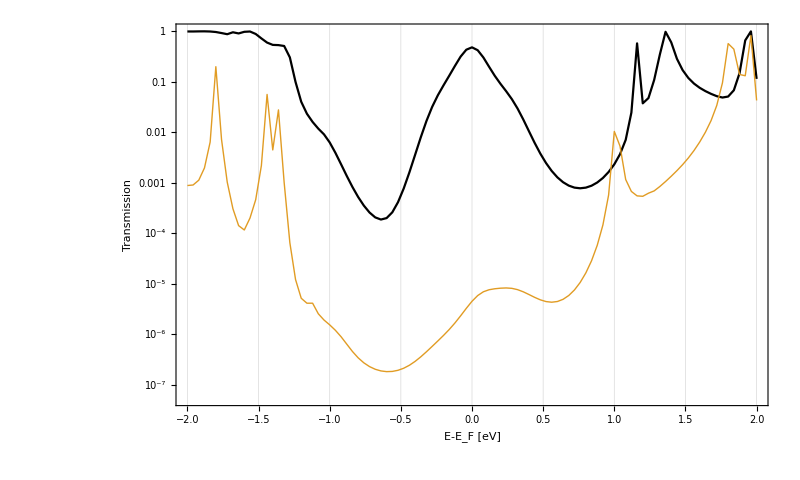

```mathematica
ListLogPlot[{et0⟦All,{1,2}⟧,et⟦All,{1,2}⟧},GridLines->{eval-EF,None},
FrameLabel->{"E-E_F [eV]"," Transmission "},
Frame->True,
AspectRatio->0.6,
(*PlotLegends->Placed[{"BZ","CJ"},{0.55,0.8}],*)
PlotRange->All,
Joined->True,
PlotStyle->{Black,Thick},
ImageSize->{800,500},
Axes->False,
styles]
```

```mathematica
evec//Dimensions
```

{210,210}

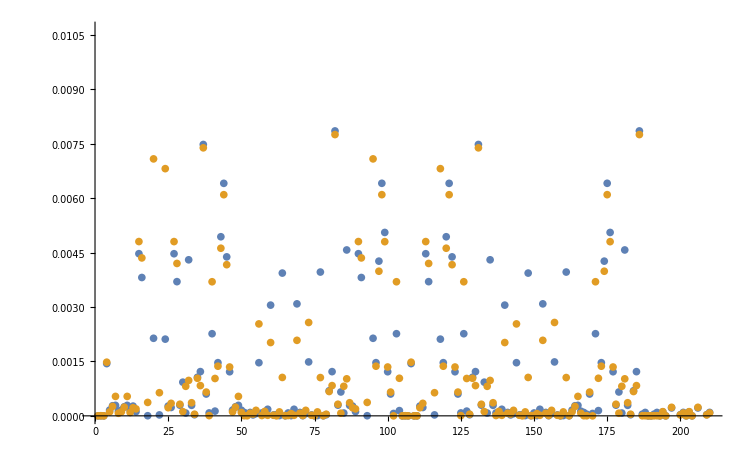

```mathematica
ListPlot[evec⟦{NHOMO,NHOMO+1}⟧^2]
```

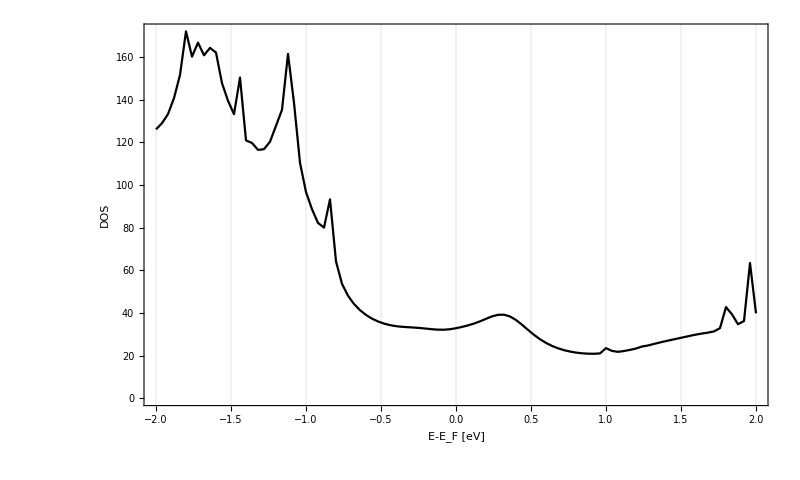

```mathematica
ListPlot[{et⟦All,{1,3}⟧},GridLines->{eval-EF,None},
FrameLabel->{"E-E_F [eV]"," DOS"},
Frame->True,
AspectRatio->0.6,
(*PlotLegends->Placed[{"BZ","CJ"},{0.55,0.8}],*)
Joined->True,
PlotStyle->{Black,Thick},
ImageSize->{800,500},
Axes->False,
styles]
```